## Governing ODE and BCs

```mathematica
eqn = D[y[x] D[y[x],x],x]*k + α* y[x]*Sin[θ] - α*Cos[θ]*y[x]*y'[x] == 1
BCs = {y[0]==1,y[1]==0.01};
```

α Sin[θ] y[x]-α Cos[θ] y[x] y'[x]+k (y'[x]^2+y[x] y''[x])==1

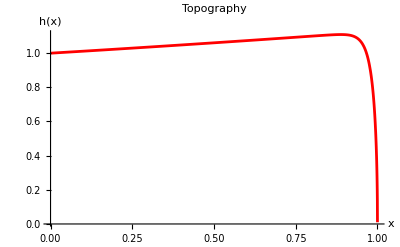

```mathematica
(*Solve numerically*)
Aval =5;(*ρg/τ - ratio of gravity to yield stress *)
(* for the analytical solution α!=2*)
thetaval = π/10;(*slope of the flow*)
kval = 0.1;(*0<k<1 - corresponds to the viscous term in the z-momentum equation*)
numSol=NDSolve[{eqn/.{α->Aval,θ->thetaval,k->kval},BCs},y[x],{x,0,1},MaxSteps->∞];
Plot[Evaluate[y[x]/. numSol],{x,0,1},AxesLabel->{"x","h(x)"},PlotStyle->Red,PlotLabel->"Topography",PlotRange->Full]
```

## Simplifying conditions

### - No internal viscous dissipation (k = 0)

α Sin[θ] y[x]-α Cos[θ] y[x] y'[x]==1

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Function[{x},(Csc[θ] (1+ProductLog[-ⅇ^(-1+(-1+x) α Sin[θ] Tan[θ])]))/α]}}

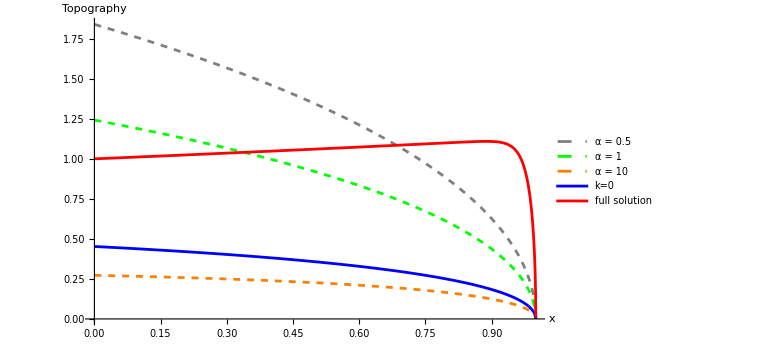

```mathematica
eqn = α* y[x]*Sin[θ] - α*Cos[θ]*y[x]*y'[x] == 1
sol = DSolve[{eqn,y[1]==0},y,{x,0,1}]
Plot[{Evaluate[Table[y[x]/. sol/. {α->a,θ->thetaval},{a,{0.5,1,10}}]],Evaluate[y[x]/.sol/. {α->Aval,θ->thetaval}],Evaluate[y[x]/. numSol]},{x,0,1},PlotStyle->{{Gray, Dashed},{Green, Dashed},{Orange,Dashed},Blue,Red},PlotLegends->{"α = 0.5","α = 1","α = 10","k=0","full solution"},AxesLabel->{"x","Topography"},ImageSize->Large]
```

### - Small slopes (θ = 0)

-α y[x] y'[x]+k (y'[x]^2+y[x] y''[x])==1

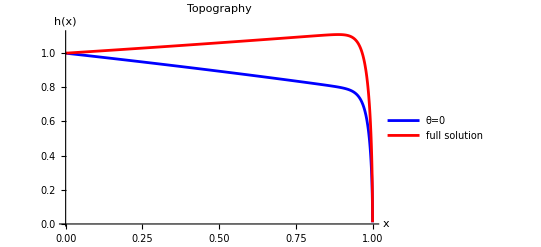

```mathematica
eqn = D[y[x] D[y[x],x],x]*k - α*y[x]*y'[x] == 1
(*Solve numerically*)
numSolt0=NDSolve[{eqn/.{α->Aval,k->kval},BCs},y[x],{x,0,1}];
Plot[{Evaluate[y[x]/. numSolt0],Evaluate[y[x]/. numSol]},{x,0,1},AxesLabel->{"x","h(x)"},PlotStyle->{Blue,Red},PlotLabel->"Topography",PlotRange->Full,PlotLegends->{"θ=0","full solution"}]
```

### - Solve the small slope problem analytically and compare with numerical solution

Note here that the α we use is actually α cosθ, we are only neglecting the sinθ term in the analytic solution

-α y[x] y'[x]+k (y'[x]^2+y[x] y''[x])==1

(√2 √(α-x α+(ⅇ^(α/k)-ⅇ^((x α)/k)) k (α/(k-ⅇ^(α/k) k))^n))/α

0.987561+0.0710104 ⅈ

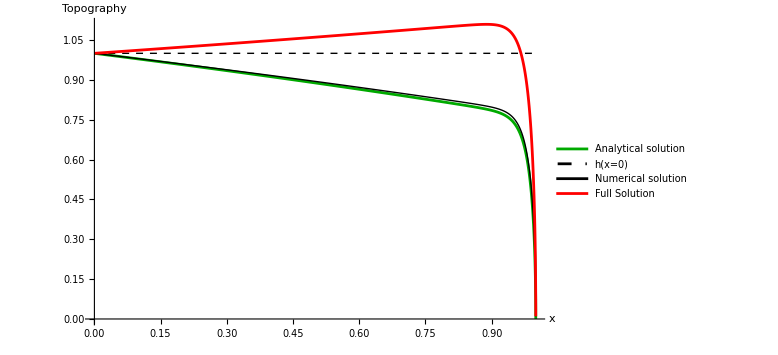

```mathematica
eqn = D[y[x] D[y[x],x],x]*k -α*y[x]*y'[x]== 1
(*solt0 = DSolve[{eqn,y[1]==0},y,{x,0,1}];*)
(*Note here that y[0] = 1/[α*Sqrt[2(α+k*exp(α/k))]]*)
ct0 = n*k/α Log[α/k/(1-Exp[α/k])]; (*this is the value of the constant for real y[x]*)
ysol = Sqrt[2k*(Exp[α/k*(1+ct0)]-Exp[α/k*(x+ct0)])-2α*(x-1)]/α//FullSimplify
(*Insert values for α,k and ζ*)
nfun = Log[1/2*(2ζ/(1-E^ζ)-α*ζ/(1-E^ζ))]/Log[ζ/(1-E^ζ)];
(*Solve for n value given α,k and ζ and boundary condition h(0) = 1, note that α!=2*)
nval = (nfun)/.{ζ->(Aval*Cos[thetaval]/kval),α->Aval*Cos[thetaval]};
N[nval]
ysol/.{α->Aval*Cos[thetaval],k->kval};
(*Compute h(0) and verify that it is indeed h(0) = 1*)
y0 = Sqrt[2/α/(ζ)*(ζ/(1-E^ζ))^n*(E^ζ-1)+2/α];
(*N[y0/.{ζ->(Aval/kval),α->Aval,n->nval}]*)
(*Plot solution*)
Plot[{Re[ysol]/.{α->Aval*Cos[thetaval],k->kval,n->nval},Re[y0]/.{ζ->Aval*Cos[thetaval]/kval,α->Aval*Cos[thetaval],n->nval},Evaluate[y[x]/. numSolt0],Evaluate[y[x]/. numSol]},{x,0,1},PlotRange->Full,AxesLabel->{"x","Topography"},PlotStyle->{Darker[Green],{Black,Thin,Dashed},{Black,Thin},Red},PlotLegends->{"Analytical solution","h(x=0)","Numerical solution","Full Solution"},PlotPoints->1000,ImageSize->Large]
```

## Attempt solving the original ODE analytically

```mathematica
eqn = D[y[x] D[y[x],x],x]*k + α* y[x]*Sin[θ] - α*Cos[θ]*y[x]*y'[x] == 1
(*solt0 = DSolve[{eqn},y,x]*)
```

α Sin[θ] y[x]-α Cos[θ] y[x] y'[x]+k (y'[x]^2+y[x] y''[x])==1